-Graphics3D-

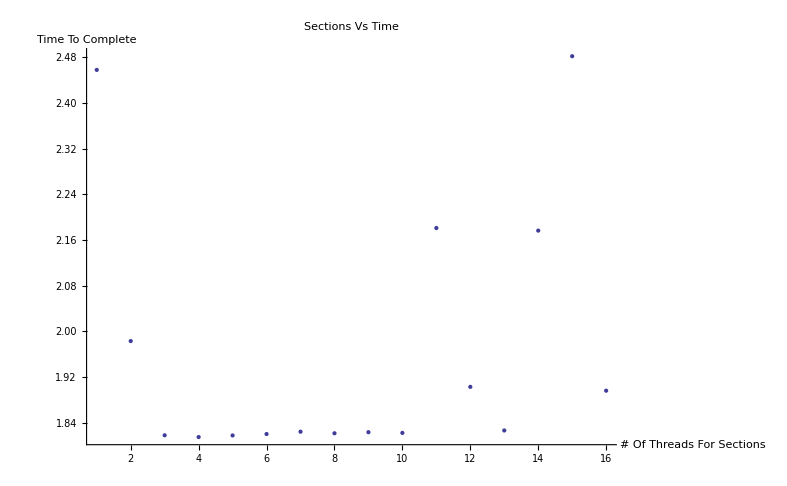

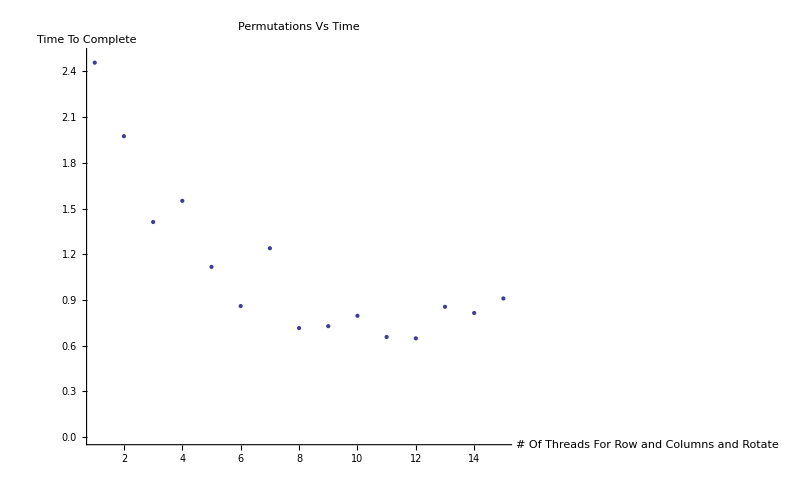

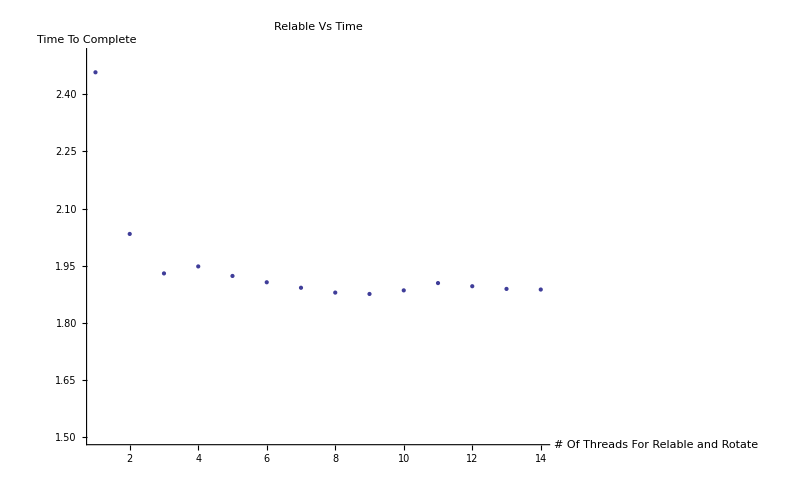

```mathematica
data = Import["C:\\Users\\Justin\\Documents\\School\\2012Spring\\Multi Core\\Assignment 3\\output.csv"];
data2 = {#[[2]],#[[3]],#[[5]]}&/@ Select[data,#[[1]]==1&];
data3={#[[1]],#[[2]],#[[5]]}&/@Select[data,(#[[3]]==1)&];
dataSe = {#[[1]],#[[5]]}&/@ Select[data,(#[[2]]==1)&&(#[[3]]==1)&];
dataCo = {#[[2]],#[[5]]}&/@ Select[data,(#[[1]]==1)&&(#[[3]]==1)&];
dataRe = {#[[3]],#[[5]]}&/@ Select[data,(#[[2]]==1)&&(#[[1]]==1)&];
ListPointPlot3D [data2,AxesLabel-> {"# Of Threads For Row And Column And Rotate","# Of Threads For Relable And Rotate","Time to Finish"},PlotLabel-> "Permutaion and Relable vs Time"]
ListPlot[dataSe,AxesLabel-> {"# Of Threads For Sections","Time To Complete"},PlotLabel->"Sections Vs Time"]
ListPlot[dataCo,AxesLabel-> {"# Of Threads For Row and Columns and Rotate","Time To Complete"},PlotLabel->"Permutations Vs Time",PlotRange->{0,2.5}]
ListPlot[dataRe,AxesLabel-> {"# Of Threads For Relable and Rotate","Time To Complete"},PlotLabel->"Relable Vs Time",PlotRange->{1.5,2.5}]
```

```mathematica
Select[data,Function[x,x[[5]]==Min[#[[5]]&/@data[[2;;]]]]][[1]]
Select[data,Function[x,x[[5]]==Min[#[[5]]&/@Select[data[[2;;]],(#[[2]]==1)&&(#[[3]]==1)&]]]][[1]]
Select[data,Function[x,x[[5]]==Min[#[[5]]&/@Select[data[[2;;]],(#[[1]]==1)&&(#[[3]]==1)&]]]][[1]]
Select[data,Function[x,x[[5]]==Min[#[[5]]&/@Select[data[[2;;]],(#[[1]]==1)&&(#[[2]]==1)&]]]][[1]]
```

{1,11,4,4084992,0.458857}

{4,1,1,4084992,1.81508}

{1,12,1,4084992,0.648182}

{1,1,9,4084992,1.87577}

```mathematica
(1/5.356267857-1)/(1/14-1)
```

0.875865

```mathematica
8*8*4084922
```

261435008